```mathematica
rawZips=Import["Desktop/puzzles-starting-2015/raw-puzzle-4-zip-codes/new-england-zip-codes.csv"];
```

{{1001,STANDARD,Agawam,,,MA,Hampden County,America/New_York,413,42.06,-72.61},2312,{6928,UNIQUE,Stamford,,International Masters Pub,CT,Fairfield County,America/New_York,203,41.09,-73.55}}
 |  |  |  |

```mathematica
rawZips[[2,1]]
zipCodes = Table[{rawZips[[i,1]], rawZips[[i,10]], rawZips[[i,11]]}, {i,1, Length[rawZips]}]
zipDisks = Table[GeoDisk[{zipCodes[[i,2]], zipCodes[[i,3]]},LinguisticAssistant], {i, 1, Length[zipCodes]}]
smallZips = Table[GeoDisk[{zipCodes[[i,2]], zipCodes[[i,3]]},LinguisticAssistant], {i, 1, 10}]
```

1002

{{1001,42.06,-72.61},{1002,42.37,-72.52},{1003,42.37,-72.52},{1004,42.37,-72.52},{1005,42.42,-72.1},{1007,42.27,-72.4},{1008,42.18,-72.93},2300,{6920,41.09,-73.55},{6921,41.09,-73.55},{6922,41.09,-73.55},{6925,41.09,-73.55},{6926,41.09,-73.55},{6927,41.09,-73.55},{6928,41.09,-73.55}}
 |  |  |  |

{GeoDisk[{42.06,-72.61},1],GeoDisk[{42.37,-72.52},1],GeoDisk[{42.37,-72.52},1],GeoDisk[{42.37,-72.52},1],GeoDisk[{42.42,-72.1},1],2304,GeoDisk[{41.09,-73.55},1],GeoDisk[{41.09,-73.55},1],GeoDisk[{41.09,-73.55},1],GeoDisk[{41.09,-73.55},1],GeoDisk[{41.09,-73.55},1]}
 |  |  |  |

```mathematica
GeoGraphics[{zipDisks}, GeoBackground->None]
```

-Graphics-

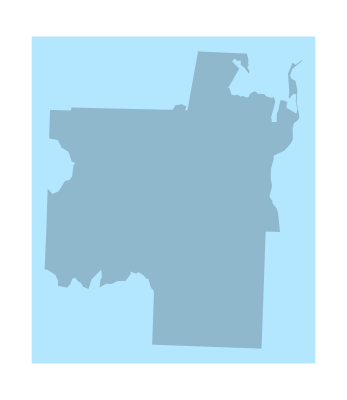

```mathematica
shelburne = ZIPCodeData["05301", "Polygon"];
GeoGraphics[shelburne, GeoBackground->RGBColor[.7, .9,1]]
```